## CellVertexCoordinates-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.5 (6-Nov-2012)) loaded Fri 9 Nov 2012 04:10:37
using xCellerator 0.90 and XSSA 1204002

```mathematica
w=TemplateRandomSquareGrid[36, {-5,-5}, {5, 5}];
```

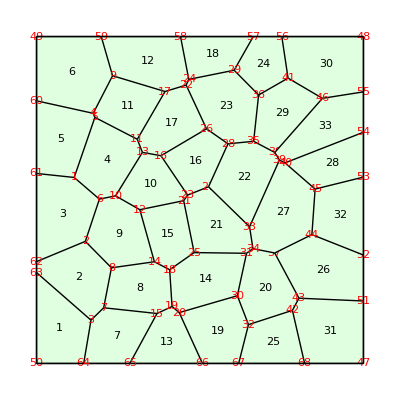

```mathematica
ShowTissue[w, "CellNumbers"-> True, "VertexNumbers"-> Red]
```

Determine the vertex numbers for cell 15

```mathematica
cvxc=CellVertexCoordinates[w,15]
```

{{-1.84018,-0.296497},{-1.3951,-1.88957},{-0.927727,-2.13339},{-0.179126,-1.60905},{-0.498747,-0.0207579}}

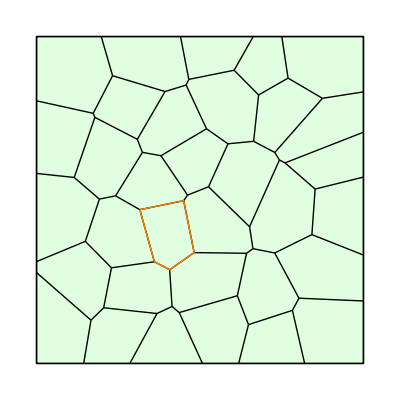

```mathematica
Show[ShowTissue[w], Boundary[cvxc, {Thick, Orange}]]
```

Determine the edge numbers for cell 15

```mathematica
c15=TissueCells[w][[15]]
```

{24,27,34,39,25}

Find the list of all edges

```mathematica
e=TissueEdges[w];
```

```mathematica
v=TissueVertices[w];
```

```mathematica
CellVertexCoordinates[c15, e, v]
```

{{-1.84018,-0.296497},{-1.3951,-1.88957},{-0.927727,-2.13339},{-0.179126,-1.60905},{-0.498747,-0.0207579}}

```mathematica
CellVertexCoordinates[w]
```

{{{-5,-5},{-3.55795,-5.},{-3.33398,-3.676},{-5.,-2.21963}},{{-5.,-1.88516},{-5.,-2.21963},{-3.33398,-3.676},{-2.94645,-3.29635},{-2.70845,-2.07378},{-3.50757,-1.26493}},{{-5.,0.811862},{-5.,-1.88516},{-3.50757,-1.26493},{-3.07705,0.0269366},{-3.84821,0.689713}},{{-3.84821,0.689713},{-3.07705,0.0269366},{-2.58216,0.127081},{-1.76067,1.45666},{-1.91756,1.85706},{-3.21481,2.52729}},{{-5.,3.03397},{-5.,0.811862},{-3.84821,0.689713},{-3.21481,2.52729},{-3.26653,2.6514}},{{-5,5},{-5.,3.03397},{-3.26653,2.6514},{-2.67397,3.80103},{-3.0206,5.}},{{-3.55795,-5.},{-2.14694,-5.},{-1.3147,-3.47219},{-2.94645,-3.29635},{-3.33398,-3.676}},{{-2.94645,-3.29635},{-2.70845,-2.07378},{-1.3951,-1.88957},{-0.927727,-2.13339},{-0.854873,-3.25698},{-1.3147,-3.47219}},{{-3.50757,-1.26493},{-3.07705,0.0269366},{-2.58216,0.127081},{-1.84018,-0.296497},{-1.3951,-1.88957},{-2.70845,-2.07378}},{{-2.58216,0.127081},{-1.84018,-0.296497},{-0.498747,-0.0207579},{-0.380254,0.150123},{-1.19412,1.35462},{-1.76067,1.45666}},{{-3.26653,2.6514},{-3.21481,2.52729},{-1.91756,1.85706},{-1.06928,3.31814},{-2.67397,3.80103}},{{-0.596027,5.},{-3.0206,5.},{-2.67397,3.80103},{-1.06928,3.31814},{-0.423603,3.51563},{-0.342636,3.68926}},{{-2.14694,-5.},{0.0755287,-5.},{-0.635382,-3.44391},{-0.854873,-3.25698},{-1.3147,-3.47219}},{{-0.927727,-2.13339},{-0.854873,-3.25698},{-0.635382,-3.44391},{1.14218,-2.92848},{1.42357,-1.62958},{-0.179126,-1.60905}},{{-1.84018,-0.296497},{-1.3951,-1.88957},{-0.927727,-2.13339},{-0.179126,-1.60905},{-0.498747,-0.0207579}},{{-1.19412,1.35462},{-0.380254,0.150123},{0.260897,0.404396},{0.8555,1.71903},{0.199513,2.17815}},{{-1.91756,1.85706},{-1.06928,3.31814},{-0.423603,3.51563},{0.199513,2.17815},{-1.19412,1.35462},{-1.76067,1.45666}},{{1.62929,5.},{-0.596027,5.},{-0.342636,3.68926},{1.04406,3.96896}},{{0.0755287,-5.},{1.18196,-5.},{1.48327,-3.81192},{1.14218,-2.92848},{-0.635382,-3.44391}},{{1.14218,-2.92848},{1.42357,-1.62958},{1.62006,-1.48937},{2.28564,-1.62008},{3.02664,-3.00352},{2.82698,-3.37582},{1.48327,-3.81192}},{{-0.498747,-0.0207579},{-0.380254,0.150123},{0.260897,0.404396},{1.5162,-0.818527},{1.62006,-1.48937},{1.42357,-1.62958},{-0.179126,-1.60905}},{{0.260897,0.404396},{0.8555,1.71903},{1.64072,1.79525},{2.28819,1.45453},{2.43004,1.22319},{1.5162,-0.818527}},{{-0.423603,3.51563},{-0.342636,3.68926},{1.04406,3.96896},{1.7927,3.21287},{1.64072,1.79525},{0.8555,1.71903},{0.199513,2.17815}},{{2.50259,5.},{1.62929,5.},{1.04406,3.96896},{1.7927,3.21287},{2.69329,3.72824}},{{1.18196,-5.},{3.20058,-5.},{2.82698,-3.37582},{1.48327,-3.81192}},{{5.,-3.08885},{5.,-1.68405},{3.42271,-1.05856},{2.28564,-1.62008},{3.02664,-3.00352}},{{1.5162,-0.818527},{1.62006,-1.48937},{2.28564,-1.62008},{3.42271,-1.05856},{3.52129,0.334576},{2.60068,1.13544},{2.43004,1.22319}},{{5.,0.700419},{5.,2.07324},{2.60068,1.13544},{3.52129,0.334576}},{{1.64072,1.79525},{1.7927,3.21287},{2.69329,3.72824},{3.74568,3.11045},{2.28819,1.45453}},{{5,5},{2.50259,5.},{2.69329,3.72824},{3.74568,3.11045},{5.,3.30749}},{{3.02664,-3.00352},{5.,-3.08885},{5,-5},{3.20058,-5.},{2.82698,-3.37582}},{{5.,-1.68405},{5.,0.700419},{3.52129,0.334576},{3.42271,-1.05856}},{{5.,2.07324},{5.,3.30749},{3.74568,3.11045},{2.28819,1.45453},{2.43004,1.22319},{2.60068,1.13544}}}